```mathematica
(* Broadband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/3 *)
(* Error < 10^-4 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.0001;
error=", error="<>ToString@err;
totalArea[rule_,sym_]:=Module[
{vars=rule/.Rule[a_,b_]->a},
area=Total[Abs[vars[[Length[vars]/2+1;;-1]]/.rule]];
If[sym,area=2area-vars[[-1]]/.rule];
area]
```

BB3; p=1, 1/2, 1/3, error=0.0001

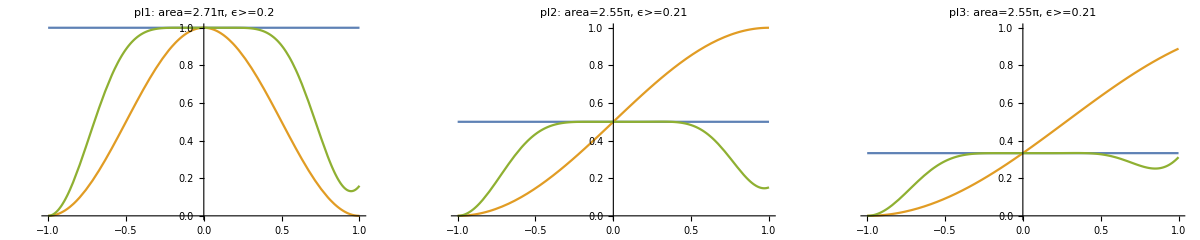

```mathematica
(*N=3*)
sequence=U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->0.92961,Δ2->0.0208,Δ3->-0.91362,Ω1->0.65564,Ω2->1.38669,Ω3->0.66928},"pl1"];
pl2=plt[1/2,{Δ1->0.23637,Δ2->0.74218,Δ3->1.03265,Ω1->1.15248,Ω2->1.00003,Ω3->0.3986},"pl2"];
pl3=plt[1/3,{Δ1->0.53801,Δ2->0.77277,Δ3->1.02718,Ω1->1.33763,Ω2->0.86102,Ω3->0.35138},"pl3"];

GGrid[Text[Style["BB3; p=1, 1/2, 1/3"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
```

BB4; p=1, error=0.0001

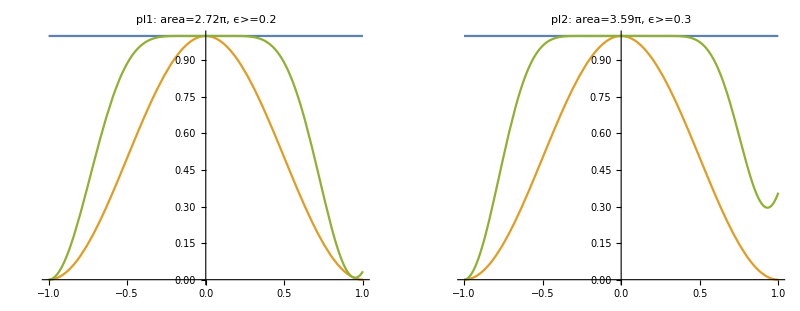

BB4; p=1/2, error=0.0001

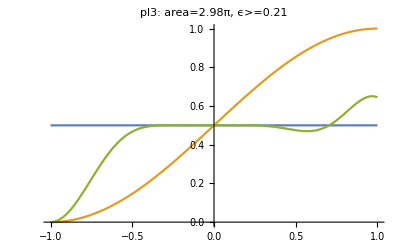

BB4; p=1/3, error=0.0001

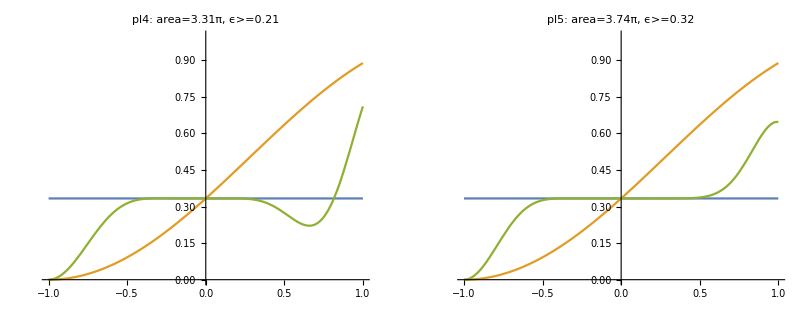

```mathematica
(*N=4*)
sequence=U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->-0.05578,Δ2->0.9479,Δ3->-0.95044,Δ4->0.12605,Ω1->0.59783,Ω2->0.76045,Ω3->0.6866,Ω4->0.67148},"pl1"];
pl2=plt[1,{Δ1->0.97707,Δ2->0.43582,Δ3->-0.31693,Δ4->-0.93969,Ω1->0.53031,Ω2->1.23633,Ω3->1.26076,Ω4->0.55878},"pl2"];

pl3=plt[1/2,{Δ1->0.09687,Δ2->0.34428,Δ3->0.75505,Δ4->1.02099,Ω1->0.84448,Ω2->0.89841,Ω3->0.87753,Ω4->0.36419},"pl3"];

pl4=plt[1/3,{Δ1->0.55172,Δ2->0.7674,Δ3->1.53395,Δ4->1.35496,Ω1->1.52675,Ω2->0.86415,Ω3->0.52453,Ω4->0.39307},"pl4"];
pl5=plt[1/3,{Δ1->0.50351,Δ2->0.58968,Δ3->0.9244,Δ4->1.05673,Ω1->1.64347,Ω2->0.98684,Ω3->0.80263,Ω4->0.30649},"pl5"];

GGrid[Text[Style["BB4; p=1"<> error,FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/2"<> error,FontSize->20]],{{pl3,Null,Null,Null}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/3"<> error,FontSize->20]],{{pl4,pl5, Null,Null}},ImageSize->Full]
```

NB5 p=1, error=0.0001

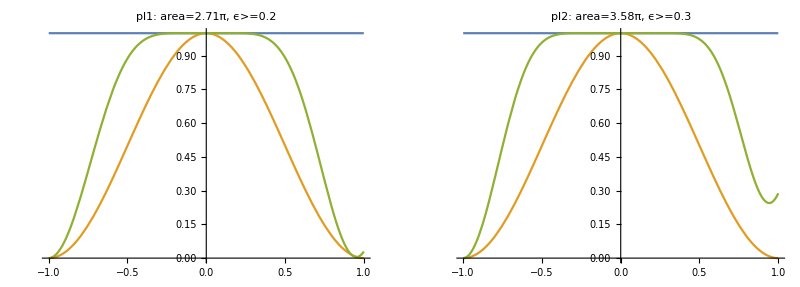

NB5 p=1/2, error=0.0001

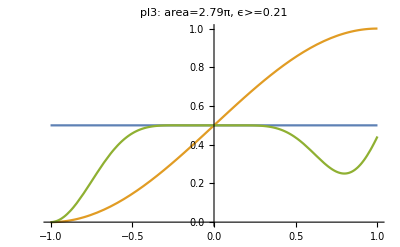

NB5 p=1/3, error=0.0001

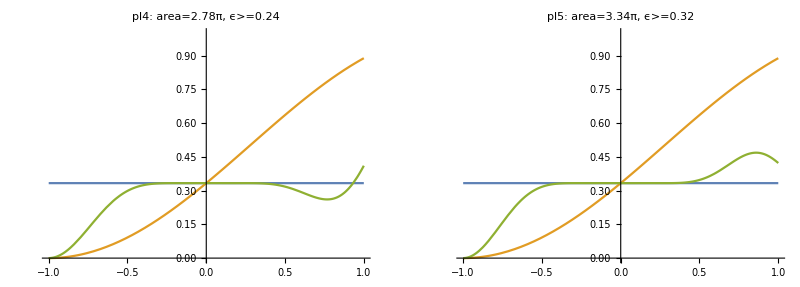

```mathematica
(*N=5*)
sequence=U[Δ5,Ω5].U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->-0.89167,Δ2->-0.07142,Δ3->0.0786,Δ4->-0.1052,Δ5->0.93282,Ω1->0.65987,Ω2->0.03348,Ω3->0.60992,Ω4->0.67724,Ω5->0.73297},"pl1"];
pl2=plt[1,{Δ1->-0.17536,Δ2->-0.40278,Δ3->-0.91304,Δ4->1.02095,Δ5->0.28358,Ω1->0.0916,Ω2->1.21365,Ω3->0.47103,Ω4->0.62508,Ω5->1.17671},"pl2"];

pl3=plt[1/2,{Δ1->0.00004,Δ2->0.19436,Δ3->0.33891,Δ4->0.52132,Δ5->1.00144,Ω1->0.18614,Ω2->0.99758,Ω3->0.58102,Ω4->0.64114,Ω5->0.38336},"pl3"];

pl4=plt[1/3,{Δ1->1.18758,Δ2->1.36633,Δ3->0.59479,Δ4->0.73831,Δ5->0.53413,Ω1->0.36846,Ω2->0.05938,Ω3->0.09306,Ω4->0.87114,Ω5->1.38575},"pl4"];
pl5=plt[1/3,{Δ1->0.99943,Δ2->0.91205,Δ3->0.64531,Δ4->0.34343,Δ5->0.45029,Ω1->0.15148,Ω2->0.48656,Ω3->0.71517,Ω4->0.63647,Ω5->1.35357},"pl5"];

GGrid[Text[Style["NB5 p=1"<> error,FontSize->20]],{{pl1,pl2,Null}},ImageSize->Full]
GGrid[Text[Style["NB5 p=1/2"<> error,FontSize->20]],{{pl3,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB5 p=1/3"<> error,FontSize->20]],{{pl4,pl5,Null}},ImageSize->Full]
```